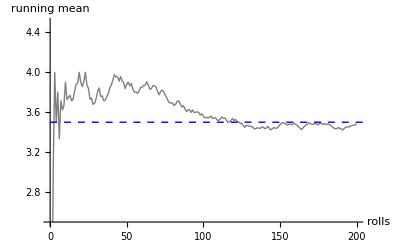

```mathematica
n = 200;
vData=RandomVariate[DiscreteUniformDistribution[{1,6}],{n}];
vMean=Accumulate[vData]/Table[i,{i,1,n}];
ListLinePlot[vMean,PlotRange->{Automatic,{2.5,4.5}},PlotStyle->Gray,Epilog->{Dashed,Blue,Line[{{0,3.5},{1000,3.5}}]},BaseStyle->{FontSize->16},AxesLabel->{"rolls ","running  mean "}]
```